### Defines the working directory and loads CmdStan.m

```mathematica
SetDirectory["~/GitHub/MathematicaStan/Examples/Bernoulli"]
Needs["CmdStan`"]
```

/home/pix/GitHub/MathematicaStan/Examples/Bernoulli

### Generates the Bernoulli Stan code and compiles it

```mathematica
stanCode="data { 
  int<lower=0> N; 
  int<lower=0,upper=1> y[N];
} 
parameters {
  real<lower=0,upper=1> theta;
} 
model {
  theta ~ beta(1,1);
  for (n in 1:N) 
    y[n] ~ bernoulli(theta);
}";
Export["bernoulli.stan",stanCode,"Text"]

(* Compile your code.
 * Caveat: this can take some time
 *)
StanCompile["bernoulli"]
```

bernoulli.stan

--- Translating Stan model to C++ code ---
bin/stanc /home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.stan --o=/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.hpp
Model name=bernoulli_model
Input file=/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.stan
Output file=/home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.hpp

--- Linking C++ model ---
g++ -I src -I stan/src -isystem stan/lib/stan_math/ -isystem stan/lib/stan_math/lib/eigen_3.2.8 -isystem stan/lib/stan_math/lib/boost_1.60.0 -isystem stan/lib/stan_math/lib/cvodes_2.8.2/include -Wall -DEIGEN_NO_DEBUG  -DBOOST_RESULT_OF_USE_TR1 -DBOOST_NO_DECLTYPE -DBOOST_DISABLE_ASSERTS -DFUSION_MAX_VECTOR_SIZE=12 -DNO_FPRINTF_OUTPUT -pipe   -lpthread  -O3 -o /home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli src/cmdstan/main.cpp -include /home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.hpp stan/lib/stan_math/lib/cvodes_2.8.2/lib/libsundials_nvecserial.a stan/lib/stan_math/lib/cvodes_2.8.2/lib/libsundials_cvodes.a

### Generates some data and saves them (RDump file)

```mathematica
n=1000;
y=Table[Random[BernoulliDistribution[0.2016]],{i,1,n}];

RDumpExport["bernoulli",{{"N",n},{"y",y}}];
```

### Runs Stan and gets result

```mathematica
StanRunSample["bernoulli"]

output=StanImport["output.csv"];
```

method = sample (Default)
  sample
    num_samples = 1000 (Default)
    num_warmup = 1000 (Default)
    save_warmup = 0 (Default)
    thin = 1 (Default)
    adapt
      engaged = 1 (Default)
      gamma = 0.050000000000000003 (Default)
      delta = 0.80000000000000004 (Default)
      kappa = 0.75 (Default)
      t0 = 10 (Default)
      init_buffer = 75 (Default)
      term_buffer = 50 (Default)
      window = 25 (Default)
    algorithm = hmc (Default)
      hmc
        engine = nuts (Default)
          nuts
            max_depth = 10 (Default)
        metric = diag_e (Default)
        stepsize = 1 (Default)
        stepsize_jitter = 0 (Default)
id = 0 (Default)
data
  file = /home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.data.R
init = 2 (Default)
random
  seed = 634367074
output
  file = /home/pix/GitHub/MathematicaStan/Examples/Bernoulli/output.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)


Gradient evaluation took 0.000134 seconds
1000 transitions using 10 leapfrog steps per transition would take 1.34 seconds.
Adjust your expectations accordingly!


Iteration:    1 / 2000 [  0%]  (Warmup)
Iteration:  100 / 2000 [  5%]  (Warmup)
Iteration:  200 / 2000 [ 10%]  (Warmup)
Iteration:  300 / 2000 [ 15%]  (Warmup)
Iteration:  400 / 2000 [ 20%]  (Warmup)
Iteration:  500 / 2000 [ 25%]  (Warmup)
Iteration:  600 / 2000 [ 30%]  (Warmup)
Iteration:  700 / 2000 [ 35%]  (Warmup)
Iteration:  800 / 2000 [ 40%]  (Warmup)
Iteration:  900 / 2000 [ 45%]  (Warmup)
Iteration: 1000 / 2000 [ 50%]  (Warmup)
Iteration: 1001 / 2000 [ 50%]  (Sampling)
Iteration: 1100 / 2000 [ 55%]  (Sampling)
Iteration: 1200 / 2000 [ 60%]  (Sampling)
Iteration: 1300 / 2000 [ 65%]  (Sampling)
Iteration: 1400 / 2000 [ 70%]  (Sampling)
Iteration: 1500 / 2000 [ 75%]  (Sampling)
Iteration: 1600 / 2000 [ 80%]  (Sampling)
Iteration: 1700 / 2000 [ 85%]  (Sampling)
Iteration: 1800 / 2000 [ 90%]  (Sampling)
Iteration: 1900 / 2000 [ 95%]  (Sampling)
Iteration: 2000 / 2000 [100%]  (Sampling)

 Elapsed Time: 0.302437 seconds (Warm-up)
               0.398076 seconds (Sampling)
               0.700513 seconds (Total)

### Uses the results

#### Lists Header

```mathematica
StanImportHeader[output]
```

{{lp__,1},{accept_stat__,2},{stepsize__,3},{treedepth__,4},{n_leapfrog__,5},{divergent__,6},{energy__,7},{theta,8}}

#### Shows sample matrix

```mathematica
Dimensions[StanImportData[output]]
Take[StanImportData[output],3]
```

{1000,8}

{{-532.463,0.693148,1.47886,1.,1.,0.,533.321,0.226882},{-532.563,0.974395,1.47886,1.,1.,0.,532.581,0.230357},{-532.629,0.982728,1.47886,1.,1.,0.,532.7,0.231909}}

#### Plots θ sample and histogram

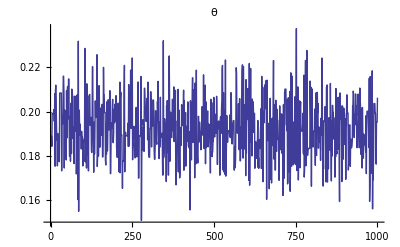

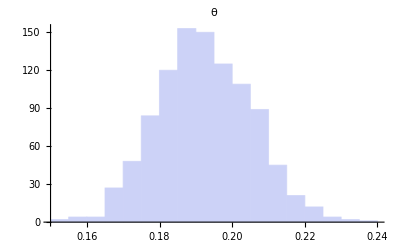

```mathematica
ListLinePlot[Flatten[StanVariableColumn["theta",output]],PlotLabel->"θ"]
Histogram[Flatten[StanVariableColumn["theta",output]],PlotLabel->"θ"]
```

### Maximimizes likelihood with StanRunOptimize

```mathematica
StanRunOptimize["bernoulli"]
```

method = optimize
  optimize
    algorithm = lbfgs (Default)
      lbfgs
        init_alpha = 0.001 (Default)
        tol_obj = 9.9999999999999998e-13 (Default)
        tol_rel_obj = 10000 (Default)
        tol_grad = 1e-08 (Default)
        tol_rel_grad = 10000000 (Default)
        tol_param = 1e-08 (Default)
        history_size = 5 (Default)
    iter = 2000 (Default)
    save_iterations = 0 (Default)
id = 0 (Default)
data
  file = /home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.data.R
init = 2 (Default)
random
  seed = 634368129
output
  file = /home/pix/GitHub/MathematicaStan/Examples/Bernoulli/output.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)

initial log joint probability = -556.075
    Iter      log prob        ||dx||      ||grad||       alpha      alpha0  # evals  Notes 
       4      -530.679    0.00430125    0.00901547           1           1        5   
Optimization terminated normally: 
  Convergence detected: relative gradient magnitude is below tolerance

#### Option manipulation

```mathematica
StanOptionOptimize[]                                            (* lists current options *)
StanSetOptionOptimize["iter",100];                              (* modifies currention options *)
StanSetOptionOptimize["output file","output_optimize.csv"];
StanOptionOptimize[]
```

{}

{{iter,100},{output file,output_optimize.csv}}

#### New run with the new options

```mathematica
StanRunOptimize["bernoulli"]
```

method = optimize
  optimize
    algorithm = lbfgs (Default)
      lbfgs
        init_alpha = 0.001 (Default)
        tol_obj = 9.9999999999999998e-13 (Default)
        tol_rel_obj = 10000 (Default)
        tol_grad = 1e-08 (Default)
        tol_rel_grad = 10000000 (Default)
        tol_param = 1e-08 (Default)
        history_size = 5 (Default)
    iter = 100
    save_iterations = 0 (Default)
id = 0 (Default)
data
  file = /home/pix/GitHub/MathematicaStan/Examples/Bernoulli/bernoulli.data.R
init = 2 (Default)
random
  seed = 634368239
output
  file = output_optimize.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)

initial log joint probability = -622.393
    Iter      log prob        ||dx||      ||grad||       alpha      alpha0  # evals  Notes 
       5      -530.679    0.00045691   0.000358764           1           1        6   
Optimization terminated normally: 
  Convergence detected: relative gradient magnitude is below tolerance

#### Overwrites and/or resets option

```mathematica
StanSetOptionOptimize["iter",100]
StanSetOptionOptimize["iter",10]
StanResetOptionOptimize[]
```

{{iter,100},{output file,output_optimize.csv}}

{{iter,10},{output file,output_optimize.csv}}

{}